# Explore and Process FBA Kernel Solutionspace

#### Copyright

© Copyright 2022 Wynand Verwoerd

This file is part of SSKernel.

The SSKernel program is free software; you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation; either version 3 of the License, or (at your option) any later version . 
This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE . See the GNU General Public License for more details . 
You should have received a copy of the GNU General Public License along with this program . If not, see http://www.gnu.org/licenses/

#### Summary

This file is meant to demonstrate how to load and analyze the output file from a SSKernel calculation that has been performed previously. It can be used as a template that can be expanded for further calculations and analysis.

It uses the variables defined in the SSKernel Configuration package and some utility functions loaded from the Centering package. Otherwise it is independent of the SSKernel code. 

The Initialization should execute automatically, by user choice, on execution of the first user command. Otherwise execute it manually first.

#### Initialize variable definitions and utility functions

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Packages"}]];
Get["Configuration`"]
Get["Centering`"]
```

### Load data

Click the Browse button to select a *.dif data file, as generated by a previous run of SSKernel.

```mathematica
FileNameSetter[Dynamic[SSKfile,(SSKfile=#;
Species=FileNameTake[SSKfile,{-2}])&],"Open",{"SSKernel output"->{"*.dif"},"All files"->{"*"}}]
```

$CellContext`SSKfileOpen

```mathematica
SSKfile
```

C:\Users\verwoerw\OneDrive - Lincoln University\My Documents\eclipse-workspace\SolutionSpaceKernel\TEST\iAB_RBC_283 SSKernel.dif

```mathematica
Clear[mainhead,SectionHeadings,importdata,KernelSpace,PeriPoints,fixvals,thindirs,rays,insphere,fixdirs, MetaboliteNames,ReactionNames, ReducedSS];importdata={KernelSpace,PeriPoints,fixvals,thindirs,rays,insphere,fixdirs, {MetaboliteNames,ReactionNames} , ReducedSS};
Evaluate[Flatten[Prepend[Table[{SectionHeadings[i],importdata[[i]]},{i,Length[importdata]}],mainhead],1]]=ToExpression/@Flatten[Import[SSKfile,"DIF","IgnoreEmptyLines"->True]];
MainHeading=DeleteCases[StringSplit[mainhead,{"(* "," *)"}],"\n"]
```

{Full SS Kernel Analysis for Test, Model iAB_RBC_283  with uncapped kernel of type Compact
 calculated on Wed 29 May 2024 in 1.33 seconds.}

### Display the imported results

#### Fixed values

Display reactions that became fixed in direction :

```mathematica
TableForm[Partition[fixdirs,UpTo[3]],TableDirections->{Column,Row,Row}]
```

EX_h2o2_e | backwards | EX_nh4_e | forwards

Now fluxes that acquire fixed values; replace flux numbers by their names for display purposes:

```mathematica
fixes=Replace[fixvals,{no_,val_}:>{ReactionNames[[no]]<>"   ",val},1];
Multicolumn[fixes,3,Appearance->Horizontal,Alignment->".",Spacings->{1,0}]
```

{EX_35cgmp_e   ,0.} | {CDS_18_1_18_2   ,0.} | {NTD2   ,0.}
{EX_3moxtyr_e   ,0.} | {CDS_18_2_16_0   ,0.} | {NMNHYD   ,0.}
{EX_4pyrdx_e   ,0.} | {CDS_18_2_18_1   ,0.} | {NTD7   ,0.}
{EX_5aop_e   ,0.} | {CEPTC_16_0_16_0   ,0.} | {NTD9   ,0.}
{EX_ac_e   ,0.} | {CEPTC_16_0_18_1   ,0.} | {NaKt   ,2.93556}
{EX_acald_e   ,0.} | {CEPTC_16_0_18_2   ,0.} | {OCDCEAt   ,0.}
{EX_acnam_e   ,0.} | {CEPTC_18_1_18_1   ,0.} | {OMPDC   ,0.}
{EX_adn_e   ,-0.01} | {CEPTC_18_1_18_2   ,0.} | {OPAH   ,0.}
{EX_adrnl_e   ,0.} | {CEPTC_18_2_16_0   ,0.} | {OROATP   ,0.}
{EX_ala__L_e   ,0.} | {CEPTC_18_2_18_1   ,0.} | {ORPT   ,0.}
{EX_bilglcur_e   ,0.} | {CEPTE_16_0_16_0   ,0.} | {PDE1   ,0.}
{EX_ca2_e   ,0.} | {CEPTE_16_0_18_1   ,0.} | {PDX5POi   ,0.}
{EX_camp_e   ,0.} | {CEPTE_16_0_18_2   ,0.} | {PDXPP   ,0.}
{EX_chol_e   ,0.} | {CEPTE_18_1_18_1   ,0.} | {PETHCT   ,0.}
{EX_cl_e   ,0.} | {CEPTE_18_1_18_2   ,0.} | {PFK   ,1.46111}
{EX_co_e   ,0.} | {CEPTE_18_2_16_0   ,0.} | {PFK26   ,0.}
{EX_cys__L_e   ,0.} | {CEPTE_18_2_18_1   ,0.} | {PGK   ,-2.92556}
{EX_dopa_e   ,0.} | {CGMPt   ,0.} | {PGL   ,0.}
{EX_etha_e   ,0.} | {CHLP   ,0.} | {PGM   ,-2.92556}
{EX_fe2_e   ,0.} | {CHLPCTD   ,0.} | {PGMT   ,0.3169}
{EX_fru_e   ,-0.0075} | {CHOLK   ,0.} | {PHETA1   ,0.}
{EX_gal_e   ,-0.3169} | {CHOLt4   ,0.} | {PHEtec   ,0.}
{EX_gam_e   ,0.} | {COt   ,0.} | {PI45P5P_16_0_16_0   ,0.}
{EX_glc__D_e   ,-1.12} | {CPPPGO   ,0.} | {PI45P5P_16_0_18_1   ,0.}
{EX_gln__L_e   ,0.} | {CYStec   ,0.} | {PI45P5P_16_0_18_2   ,0.}
{EX_gluala_e   ,0.} | {CYTK1   ,0.} | {PI45P5P_18_1_18_1   ,0.}
{EX_gly_e   ,0.} | {D_LACt2   ,0.} | {PI45P5P_18_1_18_2   ,0.}
{EX_glyc_e   ,0.} | {DAGK_hs_16_0_16_0   ,0.} | {PI45P5P_18_2_16_0   ,0.}
{EX_gthox_e   ,0.} | {DAGK_hs_16_0_18_1   ,0.} | {PI45P5P_18_2_18_1   ,0.}
{EX_hco3_e   ,5.87112} | {DAGK_hs_16_0_18_2   ,0.} | {PI45PLC_16_0_16_0   ,0.}
{EX_hcys__L_e   ,0.} | {DAGK_hs_18_1_18_1   ,0.} | {PI45PLC_16_0_18_1   ,0.}
{EX_hdca_e   ,0.} | {DAGK_hs_18_1_18_2   ,0.} | {PI45PLC_16_0_18_2   ,0.}
{EX_ins_e   ,0.} | {DAGK_hs_18_2_16_0   ,0.} | {PI45PLC_18_1_18_1   ,0.}
{EX_k_e   ,0.} | {DAGK_hs_18_2_18_1   ,0.} | {PI45PLC_18_1_18_2   ,0.}
{EX_lac__D_e   ,0.} | {DGULND   ,0.} | {PI45PLC_18_2_16_0   ,0.}
{EX_leuktrA4_e   ,0.} | {DOPAMT   ,0.} | {PI45PLC_18_2_18_1   ,0.}
{EX_leuktrB4_e   ,0.} | {DOPAtu   ,0.} | {PI4P5K_16_0_16_1   ,0.}
{EX_lnlc_e   ,0.} | {DPGM   ,0.} | {PI4P5K_16_0_18_3   ,0.}
{EX_man_e   ,-0.01} | {DPGase   ,0.} | {PI4P5K_16_0_18_4   ,0.}
{EX_mepi_e   ,0.} | {ENO   ,2.92556} | {PI4P5K_18_1_18_3   ,0.}
{EX_met__L_e   ,0.} | {ETHAK   ,0.} | {PI4P5K_18_1_18_4   ,0.}
{EX_na1_e   ,0.} | {ETHAt   ,0.} | {PI4P5K_18_2_16_0   ,0.}
{EX_nac_e   ,0.} | {ETHP   ,0.} | {PI4P5K_18_2_18_1   ,0.}
{EX_ncam_e   ,0.} | {FACOAL160   ,0.} | {PI4PLC_16_0_16_0   ,0.}
{EX_normete__L_e   ,0.} | {FACOAL181   ,0.} | {PI4PLC_16_0_18_1   ,0.}
{EX_nrpphr_e   ,0.} | {FACOAL1821   ,0.} | {PI4PLC_16_0_18_2   ,0.}
{EX_ocdcea_e   ,0.} | {FADDP   ,0.} | {PI4PLC_18_1_18_1   ,0.}
{EX_orot_e   ,0.} | {FBA   ,1.46111} | {PI4PLC_18_1_18_2   ,0.}
{EX_phe__L_e   ,0.} | {FBP26   ,0.} | {PI4PLC_18_2_16_0   ,0.}
{EX_pi_e   ,0.} | {FCLT   ,0.} | {PI4PLC_18_2_18_1   ,0.}
{EX_pydam_e   ,0.} | {FE2t   ,0.} | {PI4PP_16_0_16_0   ,0.}
{EX_pydx_e   ,0.} | {FMNAT   ,0.} | {PI4PP_16_0_18_1   ,0.}
{EX_pydxn_e   ,0.} | {FRUt1r   ,0.0075} | {PI4PP_16_0_18_2   ,0.}
{EX_ribflv_e   ,0.} | {G6PDA   ,0.} | {PI4PP_18_1_18_1   ,0.}
{EX_spmd_e   ,0.} | {G6PDH2r   ,0.} | {PI4PP_18_1_18_2   ,0.}
{EX_sprm_e   ,0.} | {GALKr   ,0.3169} | {PI4PP_18_2_16_0   ,0.}
{EX_thm_e   ,0.} | {GALOR   ,0.} | {PI4PP_18_2_18_1   ,0.}
{EX_thmmp_e   ,0.} | {GALt1r   ,0.3169} | {PIK4_16_0_16_0   ,0.}
{EX_uri_e   ,0.} | {GAMt1r   ,0.00001} | {PIK4_16_0_18_1   ,0.}
{SK_adprbp_c   ,0.} | {GAPD   ,2.92556} | {PIK4_16_0_18_2   ,0.}
{SK_akg_c   ,0.} | {GGLUCT   ,0.} | {PIK4_18_1_18_1   ,0.}
{SK_band_c   ,0.} | {GK1   ,0.} | {PIK4_18_1_18_2   ,0.}
{SK_bandmt_c   ,0.} | {GLCt1   ,1.12} | {PIK4_18_2_16_0   ,0.}
{SK_for_c   ,0.} | {GLNS   ,0.} | {PIK4_18_2_18_1   ,0.}
{SK_mi1345p_c   ,0.} | {GLNt4   ,0.} | {PIPLC_16_0_16_0   ,0.}
{SK_mi134p_c   ,0.} | {GLUCYS   ,0.} | {PIPLC_16_0_18_1   ,0.}
{SK_mi145p_c   ,0.} | {GLYCt   ,0.} | {PIPLC_16_0_18_2   ,0.}
{SK_mi14p_c   ,0.} | {GLYK   ,0.} | {PIPLC_18_1_18_1   ,0.}
{SK_pchol_hs_16_0_16_0_c   ,0.} | {GLYOX   ,0.} | {PIPLC_18_1_18_2   ,0.}
{SK_pchol_hs_16_0_18_1_c   ,0.} | {GLYt7_211_r   ,0.} | {PIPLC_18_2_16_0   ,0.}
{SK_pchol_hs_16_0_18_2_c   ,0.} | {GMPR   ,0.} | {PIPLC_18_2_18_1   ,0.}
{SK_pchol_hs_18_1_18_1_c   ,0.} | {GMPS2   ,0.} | {PIt   ,0.}
{SK_pchol_hs_18_1_18_2_c   ,0.} | {GND   ,0.} | {PLA2_2_16_0_16_0   ,0.}
{SK_pchol_hs_18_2_16_0_c   ,0.} | {GPAM_hs_16_1   ,0.} | {PLA2_2_16_0_18_1   ,0.}
{SK_pchol_hs_18_2_18_1_c   ,0.} | {GPAM_hs_18_3   ,0.} | {PLA2_2_16_0_18_2   ,0.}
{SK_pe_hs_16_0_16_0_c   ,0.} | {GPAM_hs_18_4   ,0.} | {PLA2_2_18_1_18_1   ,0.}
{SK_pe_hs_16_0_18_1_c   ,0.} | {GPDDA1   ,0.} | {PLA2_2_18_1_18_2   ,0.}
{SK_pe_hs_16_0_18_2_c   ,0.} | {GTHOXti2   ,0.} | {PLA2_2_18_2_16_0   ,0.}
{SK_pe_hs_18_1_18_1_c   ,0.} | {GTHS   ,0.} | {PLA2_2_18_2_18_1   ,0.}
{SK_pe_hs_18_1_18_2_c   ,0.} | {GUACYC   ,0.} | {PMANM   ,0.}
{SK_pe_hs_18_2_16_0_c   ,0.} | {GUAPRT   ,0.} | {PNP   ,0.}
{SK_pe_hs_18_2_18_1_c   ,0.} | {GULN3D   ,0.} | {PPA   ,0.}
{UNK3   ,0.} | {GULND   ,0.} | {PPAP_16_0_16_0   ,0.}
{3MOXTYRESSte   ,0.} | {HCO3E   ,5.87112} | {PPAP_16_0_18_1   ,0.}
{4PYRDX   ,0.} | {HCO3_CLt   ,-5.87112} | {PPAP_16_0_18_2   ,0.}
{5AOPt2   ,0.} | {HCYSte   ,0.} | {PPAP_18_1_18_1   ,0.}
{ACALDt   ,0.} | {HDCAt   ,0.} | {PPAP_18_1_18_2   ,0.}
{ACGAM2E   ,-0.0000374} | {HEX10   ,0.} | {PPAP_18_2_16_0   ,0.}
{ACGAMK   ,0.} | {HEX4   ,0.01} | {PPAP_18_2_18_1   ,0.}
{ACNAM9PL   ,0.} | {HMBS   ,0.} | {PPBNGS   ,0.}
{ACNAMPH   ,0.} | {HOXG   ,0.} | {PPM   ,0.01}
{ACNAMt2   ,0.} | {HXPRT   ,0.} | {PPPGO   ,0.}
{ACNML   ,0.0000374} | {ICDHyr   ,0.} | {PRPPS   ,0.}
{ACP1_FMN   ,0.} | {IMPD   ,0.} | {PUNP3   ,0.}
{ACt2r   ,-0.0000374} | {INSt   ,0.} | {PYAM5PO   ,0.}
{ADK1   ,0.} | {KCCt   ,-5.87112} | {PYDAMK   ,0.}
{ADMDC   ,0.} | {LEUKTRA4t   ,0.} | {PYDAMtr   ,0.}
{ADNCYC   ,0.} | {LEUKTRB4t   ,0.} | {PYDXDH   ,0.}
{ADNK1   ,0.} | {LGTHL   ,0.} | {PYDXK   ,0.}
{ADNt   ,0.01} | {LNLCt   ,0.} | {PYDXNK   ,0.}
{ADPT   ,0.} | {LPASE_16_0   ,0.} | {PYDXNtr   ,0.}
{ADRNLtu   ,0.} | {LPASE_18_1   ,0.} | {PYDXPP   ,0.}
{AGDC   ,0.} | {LPASE_18_2   ,0.} | {PYDXtr   ,0.}
{AGPAT1_16_0_16_1   ,0.} | {LTA4H   ,0.} | {PYK   ,2.92556}
{AGPAT1_16_0_18_3   ,0.} | {MAN6PI   ,0.01} | {RBFK   ,0.}
{AGPAT1_16_0_18_4   ,0.} | {MANt1r   ,0.01} | {RIBFLVt3   ,0.}
{AGPAT1_18_1_18_3   ,0.} | {MDH   ,0.} | {RIBFLVt3o   ,0.}
{AGPAT1_18_1_18_4   ,0.} | {MDRPD   ,0.} | {RNMK   ,0.}
{AGPAT1_18_2_16_0   ,0.} | {MEPIVESSte   ,0.} | {RPE   ,0.00666667}
{AGPAT1_18_2_18_1   ,0.} | {METAT   ,0.} | {RPI   ,0.00666667}
{AHCi   ,0.} | {METtec   ,0.} | {SALMCOM   ,0.}
{ALAt4   ,0.} | {MGSA   ,0.} | {SALMCOM2   ,0.}
{ALDD2x   ,0.} | {MI1345PP   ,0.} | {SPMDtex2   ,0.}
{AMANK   ,0.} | {MI145PK   ,0.} | {SPMS   ,0.}
{AMPDA   ,0.} | {MI145PP   ,0.} | {SPRMS   ,0.}
{AP4AH1   ,0.} | {MI1PP   ,0.} | {SPRMt2i   ,0.}
{ARD   ,0.} | {MI1PS   ,0.} | {TALA   ,0.00333333}
{ENOPH   ,0.} | {MTAP   ,0.} | {TDP   ,0.}
{BANDMT   ,0.} | {MTRI   ,0.} | {THMMPtrbc   ,0.}
{BILGLCURt   ,0.} | {NACt   ,0.} | {THMTP   ,0.}
{BILIRBU   ,0.} | {NADK   ,0.} | {THMtrbc   ,0.}
{BILIRED   ,0.} | {NADPN   ,0.} | {TKT1   ,0.00333333}
{CA2t   ,0.} | {NADS2   ,0.} | {TKT2   ,0.00333333}
{CAATPS   ,0.} | {NAt   ,8.80668} | {TMDPK   ,0.}
{CAMPt   ,0.} | {NCAMUP   ,0.} | {TMDPPK   ,0.}
{CDIPTr_16_0_16_0   ,0.} | {NDPK1   ,0.} | {TPI   ,1.46111}
{CDIPTr_16_0_18_1   ,0.} | {NDPK2   ,0.} | {UDPG4E   ,-0.3169}
{CDIPTr_16_0_18_2   ,0.} | {NDPK3   ,0.} | {UDPGD   ,0.}
{CDIPTr_18_1_18_1   ,0.} | {NICRNS   ,0.} | {UDPGNP   ,0.}
{CDIPTr_18_1_18_2   ,0.} | {NMNAT   ,0.} | {UMPK   ,0.}
{CDIPTr_18_2_16_0   ,0.} | {NNATr   ,0.} | {UPP3S   ,0.}
{CDIPTr_18_2_18_1   ,0.} | {NORMETEVESSte   ,0.} | {UPPDC1   ,0.}
{CDS_16_0_16_0   ,0.} | {NP1   ,0.} | {URIt   ,0.}
{CDS_16_0_18_1   ,0.} | {NRPPHRtu   ,0.} | {XYLK   ,0.}
{CDS_16_0_18_2   ,0.} | {NT5C   ,0.} | {XYLTD_D   ,0.}
{CDS_18_1_18_1   ,0.} | {NTD11   ,0.} | {XYLUR   ,0.}

#### The Kernel space specification

In the Kernel transform, the origin represents a typical, “midpoint” of the range of feasible fluxes. 
Compare it with the point that defines the centre of a maximal inscribed hypersphere  :

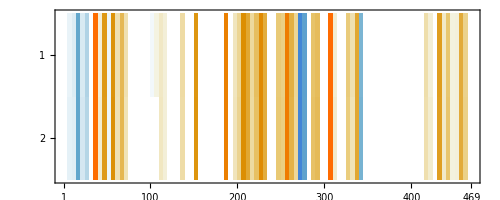

```mathematica
MatrixPlot[{KernelOrigin,insphere[[2]]},ImageSize->Full]
```

The two rows of this matrix are very similar although not identical.
The actual main flux components of this typical flux and the names of reactions they belong to, are as follows:

```mathematica
midrxns=Flatten@Position[KernelOrigin,_?(#>0.1&)];
midflux=Transpose[{Map[ReactionNames[[#]]<>"   "&,midrxns],KernelOrigin[[midrxns]]}];
Multicolumn[midflux,3,Appearance->Horizontal,Alignment->".",Spacings->{1,0}]
```

{EX_h_e   ,8.63255} | {GALKr   ,0.3169} | {ME2   ,0.484052}
{EX_hco3_e   ,5.87112} | {GALt1r   ,0.3169} | {NAt   ,8.80668}
{EX_lac__L_e   ,2.91451} | {GAPD   ,2.92556} | {NaKt   ,2.93556}
{EX_o2_e   ,2.61626} | {GLCt1   ,1.12} | {PFK   ,1.46111}
{EX_pyr_e   ,0.495141} | {GTHOr   ,0.298464} | {PGI   ,1.25131}
{CAT   ,2.61626} | {GTHPi   ,0.260896} | {PGMT   ,0.3169}
{CO2t   ,5.32554} | {H2O2t   ,5.49341} | {PYK   ,2.92556}
{DM_nadh   ,0.196639} | {H2Ot   ,0.306303} | {SBTD_D2   ,0.185588}
{ENO   ,2.92556} | {HCO3E   ,5.87112} | {SBTR   ,0.185588}
{FBA   ,1.46111} | {HEX1   ,0.934412} | {TPI   ,1.46111}
{FUM   ,0.106042} | {HEX7   ,0.193088} | {UGLT   ,0.3169}
{FUMtr   ,0.106042} | {MALt   ,0.378009} |

The second part of the Kernel transform is the set of basis vectors that span the Kernel space, and they were chosen to  point along principal axes of the Kernel space.
As vectors in the full flux space (FFS) they are as follows:

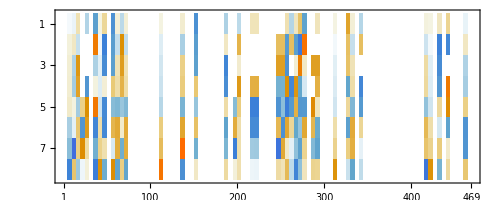

```mathematica
MatrixPlot[KernelBasis,ImageSize->Full]
```

The Kernel space itself is characterised by a set of normalised constraint vectors, specifying constraint hyperplanes by their normal directions:

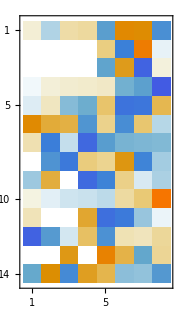

```mathematica
MatrixPlot[Kernelcons,ImageSize->Small]
```

The normal distance from the origin, for each constraint hyperplane, is given by the constraint values that make up the second part of the Kernelspace specification :

```mathematica
Multicolumn[Transpose[{Map[ToString[#]<>"   "&,Range[Length@Kernelvals]],Kernelvals}],3,Appearance->Horizontal,Spacings->{2,0}]
```

{1   ,0.173354} | {6   ,7.62293} | {11   ,0.322618}
{2   ,0.0989929} | {7   ,0.588946} | {12   ,8.83195}
{3   ,0.193761} | {8   ,0.626516} | {13   ,0.26487}
{4   ,0.0380433} | {9   ,0.528604} | {14   ,2.19316}
{5   ,0.198758} | {10   ,0.0391412} |

#### Ray vectors and thin directions

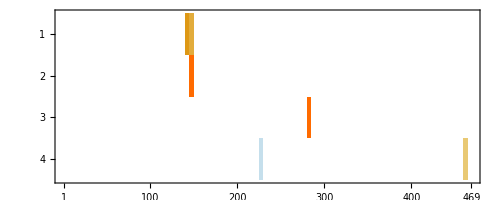

```mathematica
MatrixPlot[rays,ImageSize->Full]
```

The ray vectors form a sparse matrix by construction. The actual reactions that participate in each ray, and their amplitudes, are as follows;

```mathematica
Do[
rr=ArrayRules@SparseArray[rays];
rayrxns=Cases[rr,({ray,rxn_}->ampli_):>{ReactionNames[[rxn]],ampli}];
Print@Multicolumn[Prepend[rayrxns,"Ray no "<>ToString@ray],4,Appearance->Horizontal,Spacings->{3,0}],
{ray,Length@rays}]
```

Ray no 1 | {C160CPT1,0.707107} | {C160CPT2rbc,0.707107} |

Ray no 2 | {C181CPT1,0.707107} | {C181CPT2rbc,0.707107} |

Ray no 3 | {LNLCCPT1,0.707107} | {LNLCCPT2rbc,0.707107} |

Ray no 4 | {GALT,-0.57735} | {GALUi,0.57735} | {UGLT,0.57735}

Depending on the interactive choices made when calculating the SSK, there may are may not be directions along which the SSK considered thin enough to be flattened out. Display such direction vectors:

```mathematica
If[Length@thindirs>0,MatrixPlot[thindirs,ImageSize->Full]]
```

### Periphery Points

#### Periphery points, and utility functions for shifting between Kernel space and Flux space

The SSK constraint vectors are vectors in the low dimensional subspace in which the SSK is embedded. They are converted to FFS using the SSK basis, and then they span the hyperplane which contains the SSKernel polytope. 
Demonstrate that any thin directions are orthogonal to this hyperplane:

```mathematica
If[Length@thindirs>0,
convecs=Kernelcons.KernelBasis;
Chop[convecs.Transpose[thindirs]]]
```

The periphery points are points in FFS, that indicate the range of variation of fluxes that all share the same value for the objective function of the metabolic model.
Demonstrate that they satisfy the Kernel polytpope constraints, i.e. are all feasible:

```mathematica
And@@Map[SolutionTest[#,KernelSpace]=="Full vector in solution space"&,PeriPoints]
```

True

In FFS, where the origin lies at zero flux, the points at the periphery of the SSK all fall at similar radii, i.e. have similar overall flux, in order to produce the fixed objective values:

```mathematica
Norm/@PeriPoints
```

{23.0209,28.8943,23.9109,22.7957,22.7967,22.8439,22.8665,22.761,24.1187,23.6571,22.8884,22.8237,23.492,23.3107,23.2334,23.338,23.4003,23.8845,23.4042,23.351,23.4069,23.5228,23.4059,23.4186,23.375,23.4288,23.3819,23.3825,23.3292,23.3184,23.3596,24.8893,22.5929,23.2679,23.7355,23.7323,23.7615,23.7367,23.7123,23.2381,23.2912,23.6153,23.6435,23.3172,23.4079,23.4199,23.3713,23.3525,23.2656,23.3093,23.3609,23.3183,23.2705,23.3051,23.2927,23.3365,23.3168,23.3271,23.3265,23.3673,23.3887,23.3513}

This demonstrates that geometrically, the SSK is a (closed) volume located at a distance of about 23 flux units from the zero flux point. 
Now use one of the provided utility functions to respecify them relative to the Kernel space origin and in terms of the Kernel space basis.  The respecified vectors would be expected to have quite different lengths.

```mathematica
Dimensions[PeriPoints]
perips=DowncastPoint[PeriPoints,KernelTransform];
Dimensions@perips
```

{62,469}

{62,8}

If these projected points are transferred back to FFS, the original points are recovered (within numerical accuracy). This demonstrates that the original FFS points in fact do fall in the Kernelspace hyperplane, since the projection did not remove any vector components:

```mathematica
difs=UpliftPoint[perips,KernelTransform]-PeriPoints;
Chop[Norm/@difs]
```

{0.0000218798,0.0000186494,0.000022326,0.000019101,0,0.0000186699,0,0.0000189311,0.0000187045,0.0000188801,0.0000190662,0,0.0000186528,0,0,0,0,0.0000208566,0,0,0.0000191045,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000019101,0,0,0,0.000019101,0.000019101,0,0,0.000019101,0.000019101,0,0.000019101,0}

Relative to the new origin, they represent varying radii:

```mathematica
Norm/@perips
Min[%]
```

{12.567,10.7236,3.26422,1.54084,1.541,1.27258,1.281,1.67513,3.45424,2.0145,1.29358,1.20076,1.30059,0.528604,1.36318,0.722162,1.23866,1.81319,0.336713,0.372582,0.362089,0.464758,0.233949,0.226158,0.198758,0.305574,0.138422,0.138059,0.256351,0.129338,0.193761,4.13223,2.54725,1.07332,0.936612,0.930637,0.927717,0.912193,0.893541,0.870798,0.6624,0.660892,0.613472,0.544442,0.522341,0.516149,0.385479,0.363553,0.352207,0.327272,0.322618,0.26487,0.237446,0.227392,0.21982,0.173354,0.156118,0.134548,0.134195,0.13097,0.12572,0.0989929}

0.0989929

Compare the minimal periphery point radius above  with the radius of the maximal inscribed hypersphere:

```mathematica
insphere[[1]]
```

0.0385922

ANGULAR DISTRIBUION OF PERIPHERY POINTS

The set of peripheral points were constructed to be roughly uniformly distributed over all directions available in the kernel hyperplane.  
The simplex  in N dimensions, exhibits a perfectly uniform distribution of (N+1) directions, namely the directions of the vectors that define its vertices. The pairwise angle between any two of these directions is exactly the same, namely the angle Cos^-1[-1/N] . This gives a yardstick by which to judge how uniform the periphery directions are distributed.
Investigate that by checking the angles between all pairs of periphery points, and comparing that with the simplex single common angle value :

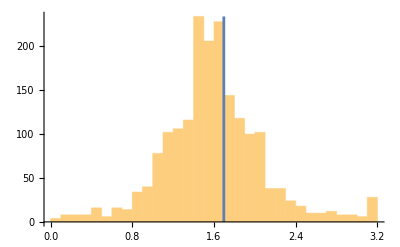

The number of directions exceeds the number of simplex directions by a factor 6.88889

```mathematica
directions=Normalize/@perips;
pairangles=Flatten@Table[ArcCos[directions[[i]].directions[[j]]],{i,1,Length@directions-1},{j,i+1,Length@directions}];
Kerneldim=Last@Dimensions[directions];
simplexangle=N@ArcCos[-1/Kerneldim];
simplexline=ListLinePlot[{{simplexangle,0},{simplexangle,Max@HistogramList[pairangles]}}];
Show[Histogram[pairangles],simplexline]
Print["The number of directions exceeds the number of simplex directions by a factor "<>TextString[Length@directions/(Kerneldim+1)]]
```

For a simplex, vertex directions are uniformly spaced and all pair angles are exactly equal (giving the blue line in the plot.).  When there are more directions than the (N+1) of the simplex, this broadens out the distribution of angles and moves the peak to a lower value.
For a roughly uniform distribution of directions, the angle between nearest neighbour directions will all be similar so represent the largest group; then a smaller group of  similar values to second nearest neighbours, etc up to a small number of directly opposing directions that give an angle value near 3.14159 radians. There should be few directions with pair angles near zero. 
The plot shows the behaviour as described. The median pair angle is similar to the simplex value, but somewhat smaller since there are  more directions.

#### Periphery points as representative fluxes

While the origin of the Kernel space serves as a single representative flux value, the set of periphery points can be useful to estimate e.g. the mean value of some function of the fluxes, or the range of variation of such a function. 
Demonstrate that idea by simply looking at individual flux values. Only a flux that varies over the Kernelspace is interesting for this, so first determine which ones they are:

```mathematica
fluxdim=Length@KernelOrigin
varfluxes=Complement[Range[fluxdim],fixvals[[All,1]]]
```

469

{8,12,13,20,22,27,36,37,38,42,46,50,57,60,65,69,75,113,114,137,138,140,145,146,147,148,152,186,200,201,220,221,226,227,248,249,251,257,258,263,266,270,271,276,277,281,282,288,293,314,328,332,341,419,420,422,433,442,443,461,465}

The identifiers and  range of variation of the variable fluxes, taken over the periphery points are

```mathematica
Multicolumn[Map[{ReactionNames[[#]]<>"   ",Min[PeriPoints[[All,#]]],Max[PeriPoints[[All,#]]]}&,varfluxes],
2,Appearance->Horizontal,Spacings->{4,0}]
```

{EX_ade_e   ,-0.014,0.01} | {FUMtr   ,-0.5,0.25}
{EX_arg__L_e   ,-0.1152,0} | {GALT   ,0,0}
{EX_ascb__L_e   ,0,0.1111} | {GALUi   ,0,0}
{EX_co2_e   ,-5.87112,-5.00592} | {GTHDH   ,0,0.1111}
{EX_dhdascb_e   ,-0.1111,0} | {GTHOr   ,0,0.75}
{EX_fum_e   ,-0.25,0.5} | {GTHPi   ,0,0.75}
{EX_h_e   ,7.90748,10.} | {H2O2t   ,0,10.}
{EX_h2o_e   ,-6.27041,4.61879} | {H2Ot   ,-4.61879,6.27041}
{EX_h2o2_e   ,-10.,0} | {HEX1   ,0.37,1.12}
{EX_hxan_e   ,0,0.024} | {HEX7   ,0.0075,0.7575}
{EX_lac__L_e   ,1.9489,3.67556} | {HYXNt   ,-0.024,0}
{EX_mal__L_e   ,-0.5,0.25} | {Ht   ,-7.07445,-4.25593}
{EX_nh4_e   ,0,0.0240474} | {L_LACt2r   ,-3.67556,-1.9489}
{EX_o2_e   ,0,5.} | {LDH_L   ,-3.67556,-1.9489}
{EX_ptrc_e   ,0,0.1152} | {LNLCCPT1   ,0,0}
{EX_pyr_e   ,0,1.7267} | {LNLCCPT2rbc   ,0,0}
{EX_urea_e   ,0,0.1152} | {MALt   ,-0.25,0.5}
{ADA   ,0,0.024} | {ME2   ,0,0.75}
{ADEt   ,-0.01,0.014} | {NH4t3r   ,0,0.0240474}
{ARGN   ,0,0.1152} | {O2t   ,-5.,0}
{ARGt5r   ,0,0.1152} | {ORNDC   ,0,0.1152}
{ASCBt   ,-0.1111,0} | {PGI   ,0.6869,1.4369}
{C160CPT1   ,0,0} | {PTRCtex2   ,0,0.1152}
{C160CPT2rbc   ,0,0} | {PUNP1   ,-0.014,0.01}
{C181CPT1   ,0,0} | {PUNP5   ,0,0.024}
{C181CPT2rbc   ,0,0} | {PYRt2   ,-1.7267,0}
{CAT   ,0,5.} | {SBTD_D2   ,0,0.75}
{CO2t   ,5.00592,5.87112} | {SBTR   ,0,0.75}
{DHAAt1r   ,0,0.1111} | {UGLT   ,0.3169,0.3169}
{DM_nadh   ,0,0.976658} | {UREAt   ,-0.1152,0}
{FUM   ,-0.5,0.25} |

These ranges are generally expected to be smaller than those obtained from a Flux Variability (FVA) calculation for the same model, because they only describe variation over a typical “central” part of the Kernelspace.

As an example of averaging, calculate the mean value of each variable flux over  all periphery points, compared with its value at the centre point:

```mathematica
Multicolumn[Map[{ReactionNames[[#]]<>"   ",Mean[PeriPoints[[All,#]]],KernelOrigin[[#]]}&,varfluxes],
2,Appearance->Horizontal,Spacings->{4,0}]
```

{EX_ade_e   ,-0.00187739,-0.00182932} | {FUMtr   ,0.106899,0.106042}
{EX_arg__L_e   ,-0.0609909,-0.0615324} | {GALT   ,0,0}
{EX_ascb__L_e   ,0.0374622,0.0375677} | {GALUi   ,0,0}
{EX_co2_e   ,-5.32703,-5.32554} | {GTHDH   ,0.0374622,0.0375677}
{EX_dhdascb_e   ,-0.0374622,-0.0375677} | {GTHOr   ,0.298269,0.298464}
{EX_fum_e   ,-0.106899,-0.106042} | {GTHPi   ,0.260807,0.260896}
{EX_h_e   ,8.63168,8.63255} | {H2O2t   ,5.49249,5.49341}
{EX_h2o_e   ,-0.307674,-0.306303} | {H2Ot   ,0.307674,0.306303}
{EX_h2o2_e   ,-5.49249,-5.49341} | {HEX1   ,0.935172,0.934412}
{EX_hxan_e   ,0.0118774,0.0118293} | {HEX7   ,0.192328,0.193088}
{EX_lac__L_e   ,2.91491,2.91451} | {HYXNt   ,-0.0118774,-0.0118293}
{EX_mal__L_e   ,-0.376198,-0.378009} | {Ht   ,-5.23491,-5.23478}
{EX_nh4_e   ,0.0119133,0.0118767} | {L_LACt2r   ,-2.91491,-2.91451}
{EX_o2_e   ,2.61584,2.61626} | {LDH_L   ,-2.91491,-2.91451}
{EX_ptrc_e   ,0.0609909,0.0615324} | {LNLCCPT1   ,0,0}
{EX_pyr_e   ,0.493784,0.495141} | {LNLCCPT2rbc   ,0,0}
{EX_urea_e   ,0.0609909,0.0615324} | {MALt   ,0.376198,0.378009}
{ADA   ,0.0118774,0.0118293} | {ME2   ,0.483097,0.484052}
{ADEt   ,0.00187739,0.00182932} | {NH4t3r   ,0.0119133,0.0118767}
{ARGN   ,0.0609909,0.0615324} | {O2t   ,-2.61584,-2.61626}
{ARGt5r   ,0.0609909,0.0615324} | {ORNDC   ,0.0609909,0.0615324}
{ASCBt   ,-0.0374622,-0.0375677} | {PGI   ,1.25207,1.25131}
{C160CPT1   ,0,0} | {PTRCtex2   ,0.0609909,0.0615324}
{C160CPT2rbc   ,0,0} | {PUNP1   ,-0.00187739,-0.00182932}
{C181CPT1   ,0,0} | {PUNP5   ,0.0118774,0.0118293}
{C181CPT2rbc   ,0,0} | {PYRt2   ,-0.493784,-0.495141}
{CAT   ,2.61584,2.61626} | {SBTD_D2   ,0.184828,0.185588}
{CO2t   ,5.32703,5.32554} | {SBTR   ,0.184828,0.185588}
{DHAAt1r   ,0.0374622,0.0375677} | {UGLT   ,0.3169,0.3169}
{DM_nadh   ,0.19548,0.196639} | {UREAt   ,-0.0609909,-0.0615324}
{FUM   ,0.106899,0.106042} |

The values closely agree in this case, because the Kernel origin was constructed as the centroid of the periphery points. The same should apply for any linear function of fluxes, but for nonlinear functions averaging the periphery points should give a different value.

#### Chords

The set of main chords of the SSK are progressively mutually orthogonal, and in directions chosen to maximize their lengths (at least approximately). They define the coordinate directions chosen for the SSK axes, and their lengths and associated aspect ratios gives and indication of the general geometric shape of the kernel polytope.
For that purpose the lengths are displayed in bar chart form in the report output file generated by the SSKernel software. However, the chords are not explicitly listed in the output data in the XYZ.dif file that forms the input for the ExploreKernel notebook.
Nevertheless, the chords can readily be recovered from this data, because the endpoints of the chords are included in the list of periphery points that were read in. It is only necessary to know which pair of periphery points belong to each chord. This information is retrieved by the utility function ChordPairs provided in the Centering.m package:

```mathematica
axpairs=ChordPairs[PeriPoints,KernelTransform]
```

{{1,2},{7,14},{6,11},{12,19},{13,16},{8,10},{5,9},{3,4}}

To construct the actual chords these pairs are used to extract each chord as a pair of endpoints:

```mathematica
chords=Map[PeriPoints[[#]]&,axpairs];
Dimensions@chords
ChordLengths=Norm@Apply[Subtract,#]&/@chords
```

{8,2,469}

{23.0199,4.29177,4.04395,2.52426,1.5425,0.585727,0.380925,0.0797469}

So there are 8 chords, each of which is a set of 2 points in the 469 dimensions of the full flux space.
To express the chords as vectors in the kernel space, they are similarly extracted from the periphery point locations as downcasted to the SSK:

```mathematica
perips=DowncastPoint[PeriPoints,KernelTransform];
chords=Map[perips[[#]]&,axpairs];
Dimensions@chords
Norm@Apply[Subtract,#]&/@chords
```

{8,2,8}

{23.0199,4.29177,4.04395,2.52426,1.5425,0.585727,0.380925,0.0797469}

Now the chord vectors are represented by vectors in just the 8 dimensions of the SSK, but of course with identical vector lengths as in the FFS representation.

### The Resampling Package

First, load the package. In this notebook, Configuration and Centering have already been loaded on startup, but in other contexts, unquoting the relevant lines would be needed.
Note that the commands listed below may need some modification if they are called from the SSKernel control panel instead of this notebook, to avoid interference with internal variables in SSKernel. For example, instead of the name ReducedSS create a differently named object such as ReducedSolutionSpace to use in the function call arguments.

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Packages"}]];
(*Get["Configuration`"]*)
(*Get["Centering`"]*)
Get["Resampling`"]
```

#### Representative fluxes on hyperplanes that intersect the solution space

Combining the SSK periphery points with the ray vectors that result from the SSK calculation, a sample set of further representative fluxes in the SS that fall in any specific hyperplane, can be generated. 
In principle, such points could alternatively be found by adding the set of constraints that define the hyperplane, to the FBA constraint set, and calculating a kernel space for this  restricted model. But the method employed here is much more efficient since it operates in a flux space with far lower dimensions. 

The simplest case would be if the intersection between the chosen hyperplane  and the solution space  is fully contained in the SSK, which is bounded by definition. Then, it would only be necessary to interpolate the known periphery points in the low dimensional SSK coordinates, to generate a point on this hyperplane. Because the SS is convex, any such interpolation is guaranteed to be feasible. 

Generally, however, the SS is unbounded and the intersection may be partially or fully outside of the SSK. This situation is dealt with by extrapolating from the periphery points using a ray vector.  This has to be done in a larger dimensional space, since it incorporates both the SSK and the ray space. However, it turns  out to be possible to do the calculation in the Reduced Solution Space (RSS), an intermediate in the SSK calculation, that excludes all fixed fluxes and prismatic rays and which thus still has much smaller dimensions than the full FBA solution space (FFS).

The definition of the SSK ensures that any feasible flux (that is, a flux point that belongs to the SS) can be reached by adding a suitable multiple of a ray vector to  a point in the SSK.  In practice, determination of the SSK often involves approximations, in which case there may be small outlying regions of the SS that cannot be reached from the approximate SSK by ray addition. Even so, the extrapolation still works to generate new sample points in the intersection of the hyperplane and the unbounded FFS, although such a sample may be less fully representative. 

The function HyperSampler in the Resampling Mathematica package loaded above, performs this combined interpolation and extrapolation to generate a new sample of points lying in the intersection. 
In fact, it is able to sample either from a strict hyperplane intersection or more generally from a subregion of the FFS that is bordered by the specified hyperplane. The next section demonstrates the relevance of hyperplane-specific sampling to bioengineering strategies aimed at e.g. enhancing the production of a specific target metabolite.  

HyperSampler accepts any known periphery point that already falls on the hyperplane as a member of the new sample, and aims to produce  a new point from each of the remaining periphery points.  However,  some such points may be infeasible or coincide, so in practice the size of the generated sample may be smaller than the original periphery point set. So in addition, given a target flux, HyperSampler also finds two additional sample points that respectively minimizes and maximises this target on the hyperplane. This guarantees that the full range of variation of the target flux is represented in the sample, despite the limited sample size and the possible absence of extrapolated sample points that fall in any  unreachable SS regions.

As an example, the list of variable fluxes in the previous section showed that the RBC model has a sink reaction that exports  water, namely EX_h2o_e  and this has flux values that range from  -6.3 to 4.6 (i.e., both import and export of water are feasible). Suppose that we want a sample of metabolic flux states for which the RBC is in equilibrium, not exchanging water with its environment. This is represented by the flux space hyperplane where component 37 of the flux vector is zero:

```mathematica
ReactionNames[[37]]
```

EX_h2o_e

The required constraint vector and value to specify this hyperplane is given as the first two arguments to HyperSampler, and the remaining arguments give the SSK specification.

```mathematica
{hpoints,hrays}=HyperSampler[{37},{0.},PeriPoints,rays,ReducedSS];
Length@PeriPoints
Length@hpoints
```

62

62

In this case the number of sample points on the hyperplane is similar to the number of periphery points from which they are derived.
These can be used to investigate which of the fluxes that vary over the SS, are significantly changed by fixing the net water transport to zero. Plot the differences, and lookup the names of those changed by more than 0.1 :

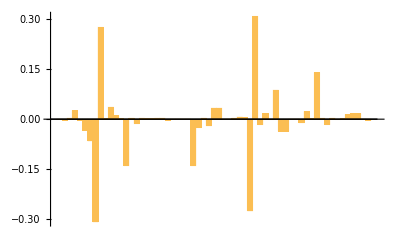

{EX_ade_e,EX_adn_e,EX_bilglcur_e,EX_fum_e,EX_h2o2_e,EX_hco3_e,EX_man_e}

```mathematica
fluxdim=Length@KernelOrigin;
varfluxes=Complement[Range[fluxdim],fixvals[[All,1]]];
difs=Mean[PeriPoints[[All,varfluxes]]]-Mean[hpoints[[All,varfluxes]]];
BarChart[difs]
ReactionNames[[Flatten@Position[difs,_?(Abs[#]>0.1&)]]]
```

Alternatively, we may be interested in the subregion of the solution space where there is a net uptake of water, i.e. flux 37 is  ≤ 0 rather than equal to zero. This requires the flux value to be specified as the pair of numbers {0., -1}.
That is because in the second argument of HyperSampler,  a single value signifies the constant value at which the flux specified by the first argument, is to be kept fixed. When given as pairs, this first member is this constant value, and the second one  being -1, 0 or 1, respectively signifies ≤ , = or ≥. The equals case is the default taken when only a single number is given.

```mathematica
{hpoints,hrays}=HyperSampler[{37},{{0.,-1}},PeriPoints,rays,ReducedSS];
Length@PeriPoints
Length@hpoints
```

62

120

This plausibly has a similar, but smaller, effect on the other fluxes as seen here

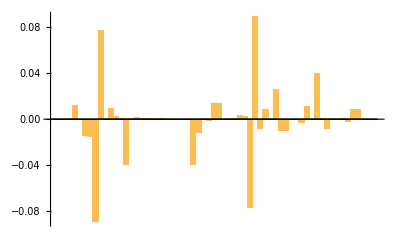

{EX_ade_e,EX_adn_e,EX_h2o2_e,EX_hco3_e}

```mathematica
fluxdim=Length@KernelOrigin;
varfluxes=Complement[Range[fluxdim],fixvals[[All,1]]];
difs=Mean[PeriPoints[[All,varfluxes]]]-Mean[hpoints[[All,varfluxes]]];
BarChart[difs]
ReactionNames[[Flatten@Position[difs,_?(Abs[#]>0.05&)]]]
```

Hypersampler also allows more complex specification of the hyperplane; instead of a single flux number, a list of fluxes may be given, fixed individually by any mixture of equalities and inequalities.  An example appears at the end of the next section. Furthermore, the constraints that determine the hyperplane orientation can be given as explicit SS vectors  instead of simply flux numbers. This allows extensive exploration of the SS through targeted sampling.

#### Resampling used to evaluate flux interventions for Bioengineering

This section demonstrates how knowledge of the solution space kernel can be used to determine fluxes that have the potential to manipulate  production or absorption of chosen target metabolites. 

A commonly used strategy for bioengineering, is to up- or downregulate the expression of particular enzymes connected with a chosen target metabolite, in order to influence its production rate. The interdependence of reactions in a metabolic network and consequent alternative pathways, makes this non-trivial and elaborate methods such as the identification of minimal cut sets (MCS) have been developed to assist in this. 

An alternative approach, rather than attempting to influence particular pathways,  is to focus on the FBA solution space, since this gives a systemic description of the metabolic range that is compatible with an overall objective such as maximizing the cellular growth rate. 

For example, knocking out a single gene so that one corresponding flux component j is set to zero, constrains the feasible flux space to the intersection of the full flux space (FFS) with the hyperplane defined by  F_j=0. 
In the case that the range of target flux values in this intersection is different from that in the FFS, production of the target metabolite will be affected. 

For example, suppose that in the FFS the target metabolite flux can range between -10 and 10. Then the production of this target should be enhanced if  a  j can be found that puts a lower limit of 5 units  for the target flux , for feasible points in the intersection.

The HyperSampler function introduced in the previous section enables this to be investigated systematically. Also included in the Resampling package, is a function TargetVariation that runs through a list of hyperplanes it is given, and for each collects data on the mean value and the range of the target metabolite on the solutionspace/hyperplane intersection. The mean is based on the resampled points and so can be considered indicative only. However, because HyperSampler directly calculates the upper and lower limits for the target flux independent of the sampling, the range value is definitive within the limits of the FBA model.

As an example, consider again the RBC model supplied as SSKernel test data. The first step is to specify a target metabolite. 

The TargetInsert function available in the Resampling package performs this function.  Given a text string that forms part of the name of the metabolite of interest, it will check if there is already a source/sink reaction for this metabolite in the stoichiometry matrix of the model (the usual case). If so, it takes this as the target flux to be monitored; if not, it adds a new column to the S matrix. In the latter case,  the SSKernel calculation needs to be rerun first for this extended model before TargetVariation can complete its resampling analysis. 

TargetInsert can also accept direct specification of the target flux, simply as the number of a column in the existing S matrix, or as an explicit flux vector.  The first option is useful when the metabolite name is ambiguous, in which case candidate column numbers are presented to the user to choose from. The second option may be used e.g. when a mixture of metabolites, in particular proportions, are to be produced by bioengineering.

TargetInsert also accepts two more optional arguments. The first is a string used as the name of the target flux, and by default this is taken as “Target: ” with the name of  any existing flux appended. When the second  optional argument is given as True, the named metabolite is to be produced (the default) or False if it is to be absorbed. It has no effect if an explicit source or sink flux is specified.

For demonstration, consider that the biological function of the red blood cell is to transport oxygen.  What would be the effect of knocking out individual genes for enzymes that control fluxes, on the oxygen export flux? To test this, take “O2” as the target.

targetcol=TargetInsert["O2"]

Loading data from input file.

Data imported from file C:\Users\verwoerw\OneDrive - Lincoln University\My Documents\eclipse-workspace\SolutionSpaceKernel\iAB_RBC_283.mat

Sink and source analysis of stoichiometry matrix.

This model has 76 metabolites identified as external, and 99 exchange reactions.

All external metabolites have either explicit sink/source reactions, or bidirectional
 exchange with the enivironment. Ticking the exemptions box in Stage 2 will have no effect.

Environmental exchange is provided for the following internal metabolites: {adprbp_c,akg_c,band_c,bandmt_c,for_c,mi1345p_c,mi134p_c,mi145p_c,mi14p_c,pchol_hs_16_0_16_0_c,pchol_hs_16_0_18_1_c,pchol_hs_16_0_18_2_c,pchol_hs_18_1_18_1_c,pchol_hs_18_1_18_2_c,pchol_hs_18_2_16_0_c,pchol_hs_18_2_18_1_c,pe_hs_16_0_16_0_c,pe_hs_16_0_18_1_c,pe_hs_16_0_18_2_c,pe_hs_18_1_18_1_c,pe_hs_18_1_18_2_c,pe_hs_18_2_16_0_c,pe_hs_18_2_18_1_c}

There are also 6 non-buffered internal metabolites, 6 of which 
each only participates in a single reaction.
All reactions that involve them will not be exempted and remain blocked 
in order to preserve the metabolic steady state.

_____________________________________________________________

The imported FBA vector is absent, zero or violates its constraints, so is ignored!

User to choose between columns {20, 38, 60}

It turns out that this is ambiguous; metabolites CO2 and H2O2 also have sink fluxes. The alert dialog produced (but not shown here) makes it clear that the last option corresponds to O2 export so rerun this with the explicit column number:

targetcol=TargetInsert[60]

60

The following may be helpful to identify target fluxes of interest, where there is no clearcut biochemical consideration. Only variable fluxes are open to be manipulated, and of those the ones that export a metabolite are the most straightforward to consider as  they do not need an extra flux to be added and SSKernel consequently to be rerun. For many models the export fluxes are identified by their names beginning with “EX” or ending in “_e”; else modify the code as appropriate.

```mathematica
cols=Length@ReducedSS[[2,1]];
nonfixes=Complement[Range[cols],fixvals[[All,1]]];
Print["There are a total of "<>ToString[cols]<>" fluxes of which "<>ToString[Length@nonfixes]<>" have varying values over the solution space for the optimized FBA objective."];
(*ReactionNames[[nonfixes]]*)
Print["Of these, the following appear to be export fluxes: \n"<>ToString[Intersection[Flatten@StringCases[ReactionNames,{__~~"_e","EX_"~~__}],ReactionNames[[nonfixes]]]]];
```

There are a total of 469 fluxes of which 61 have varying values over the solution space for the optimized FBA objective.

Of these, the following appear to be export fluxes: 
{EX_ade_e, EX_arg__L_e, EX_ascb__L_e, EX_co2_e, EX_dhdascb_e, EX_fum_e, EX_h2o2_e, EX_h2o_e, EX_h_e, EX_hxan_e, EX_lac__L_e, EX_mal__L_e, EX_nh4_e, EX_ptrc_e, EX_pyr_e, EX_urea_e, Target: EX_o2_e}

The following code sets up a list of hyperplanes, each of which corresponds with one of the fluxes that remain variable over the RBC solution space, and sets it to zero.  Then the function TargetVariation calculates statistics for the sample points on each of these hyperplane intersections with the solution space, and the result is displayed in  a table.

```mathematica
(* Set up the list of hyperplanes to be sampled, as each variable flux in turn fixed to zero*)
cols=Length@ReducedSS[[2,1]];
nonfixes=Complement[Range[cols],fixvals[[All,1]]];hyperlist=Partition[nonfixes,1];
valuelist=ConstantArray[{0},Length@hyperlist] ;         
(* Sample each hyperplane and collect data on target flux *)
Timing[samples=TargetVariation[hyperlist,valuelist,PeriPoints,rays,ReducedSS,targetcol,False];]
```

Number of distinct sample points, across all 61 probed hyperplanes: 758

TRIAL
No | ASSIGNED 
Fluxes | 
Values | SAMPLE
Count | TARGET
Mean | 
Lower | 
Upper
1 | SS Kernel | -- | 64 | 2.61 | 0 | 5.
  |   |   |   |   |   |  
2 | {EX_ade_e} | {0} | 64 | 3.25 | 0 | 5.
3 | {ME2} | {0} | 4 | 3.19 | 0 | 5.
4 | {ADEt} | {0} | 64 | 3.13 | 0 | 5.
5 | {PUNP1} | {0} | 64 | 3.13 | 0 | 5.
6 | {FUMtr} | {0} | 64 | 3.02 | 0 | 5.
7 | {FUM} | {0} | 64 | 3.02 | 0 | 5.
8 | {EX_fum_e} | {0} | 64 | 3.01 | 0 | 5.
9 | {UREAt} | {0} | 10 | 2.77 | 0 | 5.
10 | {PTRCtex2} | {0} | 10 | 2.77 | 0 | 5.
11 | {ORNDC} | {0} | 10 | 2.77 | 0 | 5.
12 | {ARGt5r} | {0} | 10 | 2.77 | 0 | 5.
13 | {ARGN} | {0} | 10 | 2.77 | 0 | 5.
14 | {EX_urea_e} | {0} | 10 | 2.77 | 0 | 5.
15 | {EX_ptrc_e} | {0} | 10 | 2.77 | 0 | 5.
16 | {EX_arg__L_e} | {0} | 10 | 2.77 | 0 | 5.
17 | {SBTR} | {0} | 14 | 2.76 | 0 | 5.
18 | {SBTD_D2} | {0} | 14 | 2.76 | 0 | 5.
19 | {H2Ot} | {0} | 64 | 2.75 | 2.32 | 3.14
20 | {EX_h2o_e} | {0} | 64 | 2.75 | 2.32 | 3.14
21 | {GTHPi} | {0} | 13 | 2.7 | 0 | 5.
22 | {MALt} | {0} | 64 | 2.69 | 0 | 5.
23 | {EX_mal__L_e} | {0} | 64 | 2.69 | 0 | 5.
24 | {PUNP5} | {0} | 17 | 2.68 | 0 | 5.
25 | {NH4t3r} | {0} | 17 | 2.68 | 0 | 5.
26 | {HYXNt} | {0} | 17 | 2.68 | 0 | 5.
27 | {ADA} | {0} | 17 | 2.68 | 0 | 5.
28 | {EX_nh4_e} | {0} | 17 | 2.68 | 0 | 5.
29 | {EX_hxan_e} | {0} | 17 | 2.68 | 0 | 5.
30 | {GTHOr} | {0} | 8 | 2.66 | 0 | 5.
31 | {LNLCCPT2rbc} | {0} | 64 | 2.61 | 0 | 5.
32 | {LNLCCPT1} | {0} | 64 | 2.61 | 0 | 5.
33 | {GALUi} | {0} | 64 | 2.61 | 0 | 5.
34 | {GALT} | {0} | 64 | 2.61 | 0 | 5.
35 | {C181CPT2rbc} | {0} | 64 | 2.61 | 0 | 5.
36 | {C181CPT1} | {0} | 64 | 2.61 | 0 | 5.
37 | {C160CPT2rbc} | {0} | 64 | 2.61 | 0 | 5.
38 | {C160CPT1} | {0} | 64 | 2.61 | 0 | 5.
39 | {GTHDH} | {0} | 20 | 2.59 | 0 | 5.
40 | {DHAAt1r} | {0} | 20 | 2.59 | 0 | 5.
41 | {ASCBt} | {0} | 20 | 2.59 | 0 | 5.
42 | {EX_dhdascb_e} | {0} | 20 | 2.59 | 0 | 5.
43 | {EX_ascb__L_e} | {0} | 20 | 2.59 | 0 | 5.
44 | {DM_nadh} | {0} | 10 | 2.35 | 0 | 5.
45 | {PYRt2} | {0} | 5 | 2.21 | 0 | 5.
46 | {EX_pyr_e} | {0} | 5 | 2.21 | 0 | 5.
47 | {O2t} | {0} | 2 | 0 | 0 | 0
48 | {H2O2t} | {0} | 2 | 0 | 0 | 0
49 | {CAT} | {0} | 2 | 0 | 0 | 0
50 | {Target: EX_o2_e} | {0} | 2 | 0 | 0 | 0
51 | {EX_h2o2_e} | {0} | 2 | 0 | 0 | 0
52 | {UGLT} | {0} | 0 | -- | -- | --
53 | {PGI} | {0} | 0 | -- | -- | --
54 | {LDH_L} | {0} | 0 | -- | -- | --
55 | {L_LACt2r} | {0} | 0 | -- | -- | --
56 | {Ht} | {0} | 0 | -- | -- | --
57 | {HEX7} | {0} | 0 | -- | -- | --
58 | {HEX1} | {0} | 0 | -- | -- | --
59 | {CO2t} | {0} | 0 | -- | -- | --
60 | {EX_lac__L_e} | {0} | 0 | -- | -- | --
61 | {EX_h_e} | {0} | 0 | -- | -- | --
62 | {EX_co2_e} | {0} | 0 | -- | -- | --Variation of Target Flux (Target: EX_o2_e) in Response to Assigning Flux Values.

{8.54688,Null}

This table illustrates several cases that can occur. For example, the last line shows that blocking CO2 export makes the metabolic state infeasible, so there are zero sample points and no statistics; several other fluxes behave similarly. 
Next higher up, blocking export of H2O2 remains feasible, but only with zero export of the O2 target and with only two sample points (the minimum and maximum, possibly coinciding).
Blocking most other variable fluxes leaves the range of the target flux unchanged, compared to the full solution space as shown in the first line of the table for comparison purposes. In some of these cases, though, the mean target flux is shifted up or down, suggesting that downregulation may achieve a desired effect.
The most promising intervention however, seems to be downregulating either the H2Ot or EX_h20_e reactions since that forces O2 export by restricting the target flux to a narrower positive range around the middle of what is allowed by the full solution space.
The chemical reaction formulas for a reaction can be inspected by using the Formula function supplied in the  Resampling package:

```mathematica
Formula["H2Ot"]
Formula["EX_h2o_e"]
```

H2Ot: h2o_e ⟶ h2o_c

EX_h2o_e: h2o_e ⟶

The Formula function accepts either a character string contained in a reaction name, or a number or list of numbers that specify the column position of the reaction(s) in the stoichiometry matrix.

TargetVariation returns the actual sampled points, and in the call above they are available in the array samples for further investigation. This array contains a sublist of sample points for each of the hyperplanes represented in the table, in the same order as it appears in the table. For example, knocking out the reaction named “CAT” is line 49 in the table, and yielded 2 distinct sample points:

```mathematica
Length@samples[[49]]
Norm[samples[[49,1]]-samples[[49,2]]]
```

2

3.53921

The fact that there are only 2 sample points suggests that in this case the feasible space reduced to a single line, and the sample points are presumably the extremes where the line intersects the boundary of the solution space. That can be tested by checking if a small extension of the connecting line between the sample pair in either direction gives infeasible points:

```mathematica
point1=samples[[49,1]];
point2=samples[[49,2]];
point3=point2+0.01(point2-point1);
point4=point1+0.01(point1-point2);
SolutionTest[#,KernelSpace]&/@{point1,point2,point3,point4}
```

{Full vector in solution space,Full vector in solution space,Vector violates constraints by {0, 0, 0, 0, 0, 0, 0, 0, -0.0213623, 0, 0, 0, 0, 0},Vector violates constraints by {0, 0, 0, 0, 0, 0, 0, -0.0180237, 0, 0, 0, 0, 0, 0}}

So indeed the samples are feasible but the extensions are not. 
This is merely an example of working with the sample points.

The demonstrated use of the TargetVariation function, to systematically check all single gene knockouts of all reactions for which flux variation is compatible with the fixed FBA objective, is just an illustration.  For large metabolic models, particularly if they have a large set of variable fluxes, this may become cumbersome. A more targeted approach based on specific biochemical knowledge, for example based on a minimal cut set (MCS) analysis, would be more appropriate. 

It is noted that the HyperSampler and TargetVariation functions allow far more complex specifications of the hyperplanes or solution space regions to be sampled, to facilitate this.  A nearly trivial extension is that  flux values may be fixed to any value, not just zero. More significantly, multiple fluxes can be fixed simultaneously. Also, these or a subset of them may be restricted to a range of values rather than a fixed value. An example of how to use inequalities in the hyperplane specification for HyperSampler was given in the previous section on representative fluxes. This applies equally well to TargetVariation since it passes the hyperplane specification through to HyperSampler. 
The following demonstrates setting up  hyperplanes with a variety of flux value specifications, including a case with multiple fluxes and a mix of equalities and inequalities.

```mathematica
hyperlist={{20},{20,22,27},{249}};
valuelist={{-5.3},{{-5.3,1},-0.05,{-0.2,-1}},{{0.35,0}}};
```

```mathematica
Timing[samples=TargetVariation[hyperlist,valuelist,PeriPoints,rays,ReducedSS,targetcol,False];]
```

Number of distinct sample points, across all 3 probed hyperplanes: 310

TRIAL
No | ASSIGNED 
Fluxes | 
Values | SAMPLE
Count | TARGET
Mean | 
Lower | 
Upper
1 | SS Kernel | -- | 64 | 2.61 | 0 | 5.
  |   |   |   |   |   |  
2 | {EX_co2_e} | {-5.3} | 64 | 2.57 | 0 | 5.
3 | {EX_co2_e, EX_dhdascb_e, EX_fum_e} | {≥ -5.3,-0.05,≤ -0.2} | 118 | 2.54 | 0 | 5.
4 | {GTHOr} | {0.35} | 64 | 2.41 | 0 | 4.88Variation of Target Flux (Target: EX_o2_e) in Response to Assigning Flux Values.

{1.04688,Null}

Note that for routine application of HyperSampler and TargetVariation, running them in a text based commandline environment may be more convenient. A special batch file and Wolfram language script is provided as part of the SSKernel software for this purpose, and the specification of the target and hyperplanes to be sampled are put in a special input file when these are used ; see the manual.